### Constants

```mathematica
filters={"Blue","Yellow","Red","NoFilter"};
colorFilters=filters[[;;3]];
color=<|"NoFilter"->(Gray&),"Red"->(Red&),"Blue"->(Blue&),"Yellow"->(Yellow&)|>;
samples={"White","BK7","SF58"};
magnetism={5,-90,-166,-259,-5};
```

### Malus Law

```mathematica
FitMalusFull[filter_]:=
Module[{rawData,n,chunks,μ,σ,around,angles},
rawData=Rest[Import[NotebookDirectory[]<>"Malus"<>filter<>".xlsx","XLSX"][[1]]]ᵀ[[2]];
n=Length@rawData/10-1;
{μ,σ}=Table[#@rawData[[10i+1;;10i+10]]&/@{Mean,StandardDeviation},{i,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
angles=Range[0,10n+1,10]°;
fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ-Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)];
Print[fit];
Print[fit["ParameterTable"]];
Print@Show[
ListPlot[{angles,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,0,angles[[-1]]},ColorFunction->color[filter]]
]
]
```

FittedModel[-0.0015013-0.0385886 Cos[1.10467-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.0015013 | 0.000017872 | -84.0031 | 5.10037×10^-41
m_2 | 0.0385886 | 0.0000206507 | 1868.63 | 8.63509×10^-87
m_3 | 1.10467 | 0.00049499 | 2231.71 | 2.06263×10^-89

{0,10 °,20 °,30 °,40 °,50 °,60 °,70 °,80 °,90 °,100 °,110 °,120 °,130 °,140 °,150 °,160 °,170 °,180 °,190 °,200 °,210 °,220 °,230 °,240 °,250 °,260 °,270 °,280 °,290 °,300 °,310 °,320 °,330 °,340 °,350 °,360 °}

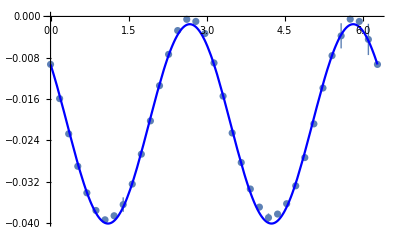

```mathematica
FitMalusFull["Blue"]
```

FittedModel[-0.0015013-0.0385886 Cos[1.10467-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.0015013 | 0.000017872 | -84.0031 | 5.10037×10^-41
m_2 | 0.0385886 | 0.0000206507 | 1868.63 | 8.63509×10^-87
m_3 | 1.10467 | 0.00049499 | 2231.71 | 2.06263×10^-89

Part::partd: Part specification {-0.00806858,-0.00933564,-0.00949422,-0.00941278,-0.00947995,-0.00942895,-0.00940849,-0.00934266,-0.0093443,-0.00944941,«360»}⟦-1,1⟧ is longer than depth of object.

{-0.00806858,-0.00933564,-0.00949422,-0.00941278,-0.00947995,-0.00942895,-0.00940849,-0.00934266,-0.0093443,-0.00944941,-0.0159206,-0.0158078,-0.0158726,-0.0159089,-0.0159265,-0.0159049,-0.0159405,-0.0159338,-0.0159014,-0.0159279,-0.0228457,-0.0229095,-0.0228665,-0.0219327,-0.0227725,-0.0226227,-0.0226605,-0.0227536,-0.0228014,-0.0230077,-0.0287525,-0.0286982,-0.0285358,-0.0287225,-0.0290384,-0.0291832,-0.0292609,-0.0292659,-0.0292714,-0.0293102,-0.0341367,-0.0341226,-0.0341517,-0.0341378,-0.0341567,-0.0341519,-0.0341646,-0.0341589,-0.0341618,-0.034149,-0.037501,-0.0374481,-0.0376244,-0.0376067,-0.0376093,-0.0375491,-0.0375958,-0.0375483,-0.0375491,-0.0375493,-0.039464,-0.0396059,-0.0397594,-0.0396989,-0.0397393,-0.0395114,-0.0392169,-0.038998,-0.038472,-0.0391831,-0.0385953,-0.0385211,-0.0387166,-0.038388,-0.0385948,-0.0385808,-0.0385913,-0.0385475,-0.0386288,-0.0386567,-0.0363531,-0.0342725,-0.0352475,-0.036854,-0.036225,-0.0360769,-0.0351137,-0.0376451,-0.0391621,-0.0372495,-0.0323325,-0.0323707,-0.0323571,-0.0323175,-0.0324236,-0.032356,-0.0326002,-0.0328577,-0.0326399,-0.0322489,-0.0267275,-0.0267556,-0.0267981,-0.0268257,-0.0269801,-0.0272659,-0.0271109,-0.0263197,-0.0259328,-0.0258712,-0.0205403,-0.0203028,-0.0201354,-0.0200936,-0.0201124,-0.0201664,-0.0201969,-0.0202285,-0.0202152,-0.0201567,-0.0134408,-0.013366,-0.0135342,-0.0133968,-0.0134295,-0.01332,-0.0131828,-0.0131992,-0.0134075,-0.0137055,-0.00727714,-0.0073491,-0.00726419,-0.00744024,-0.00743803,-0.00737631,-0.00719311,-0.00708595,-0.0073691,-0.00757034,-0.00271332,-0.00271849,-0.00272398,-0.00272185,-0.00274301,-0.00274293,-0.00253089,-0.00266462,-0.00303819,-0.00267769,-0.000219034,-0.000539577,-0.00103488,-0.000545681,-0.000713353,-0.000542335,-0.000218574,-0.00159206,3.831×10^-6,-0.000166063,-0.000697965,-0.000346148,-0.000805567,-0.00245664,-0.00118835,-0.000545605,-0.000751791,-0.000931506,-0.000993967,-0.000875815,-0.00202182,-0.00310083,-0.00327568,-0.00332974,-0.0035786,-0.00346377,-0.00367302,-0.00350636,-0.00318197,-0.0039444,-0.00884234,-0.00864111,-0.00957528,-0.00911079,-0.00854491,-0.00918033,-0.00994413,-0.00847729,-0.00797768,-0.00972638,-0.0155183,-0.0149726,-0.0153481,-0.0153807,-0.0154577,-0.0154298,-0.0155289,-0.0154659,-0.0156383,-0.0155041,-0.0216877,-0.021782,-0.0222318,-0.0221814,-0.0233599,-0.0227567,-0.0233464,-0.0229678,-0.0225469,-0.0227033,-0.0280366,-0.0278925,-0.0281785,-0.028029,-0.0282204,-0.0287202,-0.0287427,-0.0284646,-0.0281415,-0.0283581,-0.0335667,-0.0332455,-0.0333885,-0.0333912,-0.033393,-0.0334296,-0.0334164,-0.0333756,-0.0333192,-0.0334911,-0.0370572,-0.0373367,-0.0372242,-0.0368759,-0.0368832,-0.0368209,-0.0368825,-0.0367828,-0.0367361,-0.0364662,-0.0374276,-0.0378529,-0.0386225,-0.0392532,-0.0401519,-0.0397729,-0.039203,-0.0389925,-0.0391181,-0.0390909,-0.0382163,-0.0381765,-0.0381907,-0.038253,-0.0382613,-0.0382595,-0.0382397,-0.0382691,-0.0383363,-0.0383478,-0.0362281,-0.0363598,-0.0364706,-0.036361,-0.0363272,-0.036435,-0.0365401,-0.0363102,-0.0356077,-0.0358703,-0.032919,-0.0327944,-0.0328186,-0.0326999,-0.0327839,-0.0328024,-0.0328769,-0.032662,-0.0327302,-0.0327789,-0.0273501,-0.0274096,-0.0273601,-0.0274121,-0.0273054,-0.0272348,-0.0272253,-0.0270062,-0.0272947,-0.0275926,-0.0206787,-0.0207571,-0.0208795,-0.0208148,-0.0207959,-0.0208819,-0.0207778,-0.0207925,-0.0208112,-0.0207487,-0.013795,-0.0137025,-0.0137018,-0.0138268,-0.0138033,-0.0137786,-0.0139543,-0.0140037,-0.0140748,-0.0138677,-0.00766411,-0.00732347,-0.00744462,-0.00745592,-0.00762053,-0.00778889,-0.00770052,-0.00763635,-0.00763035,-0.00759148,-0.00390507,-0.00416311,-0.0101159,-0.00478642,-0.00246325,-0.00162614,-0.00226276,-0.00296628,-0.00271067,-0.00250371,-0.000472917,-0.000418899,-0.000541761,-0.000589789,-0.000415081,-0.000414085,-0.000613133,-0.000539679,-0.000613963,-0.000596149,-0.00094388,-0.000890897,-0.000967747,-0.000955858,-0.000930063,-0.000985832,-0.000946907,-0.000832805,-0.00131242,-0.000854387,0.00231536,-0.00299585,-0.00859915,-0.00646003,-0.0022546,-0.00376725,-0.0048236,-0.00681416,-0.00537801,-0.00566975,-0.00929263,-0.00928335,-0.00929234,-0.00928905,-0.00928769,-0.00928929,-0.00928083,-0.00928451,-0.00928015,-0.00927821}⟦-1,1⟧

Part::partd: Part specification {-0.00806858,-0.00933564,-0.00949422,-0.00941278,-0.00947995,-0.00942895,-0.00940849,-0.00934266,-0.0093443,-0.00944941,«360»}⟦-1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value {-0.00806858,-0.00933564,-0.00949422,-0.00941278,-0.00947995,-0.00942895,-0.00940849,-0.00934266,-0.0093443,-0.00944941,«360»}⟦-1,1⟧ in {θ,0,{-0.00806858,-0.00933564,-0.00949422,-0.00941278,-0.00947995,-0.00942895,-0.00940849,-0.00934266,-0.0093443,-0.00944941,«360»}⟦-1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

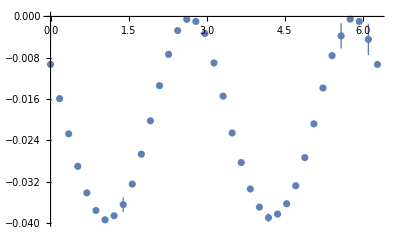
Show[-Graphics-,Plot[Normal[fit],{θ,0,rawData$518600⟦-1,1⟧},ColorFunction→color[Blue]]]

```mathematica
FitMalusFull[filters[[1]]]
```

FittedModel[-0.00061743-0.0390204 Cos[1.10733-θ]^2]

| Estimate | Standard Error | t-Statistic | P-Value
m_1 | -0.00061743 | 6.10432×10^-6 | -101.146 | 9.46303×10^-44
m_2 | 0.0390204 | 0.0000179432 | 2174.67 | 4.97455×10^-89
m_3 | 1.10733 | 0.000241489 | 4585.45 | 4.79912×10^-100

Plot::plln: Limiting value data⟦-1,1⟧ in {θ,0,data⟦-1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

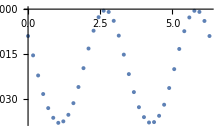
Show[-Graphics-,Plot[Normal[fit],{θ,0,data⟦-1,1⟧},ColorFunction→color[Yellow]]]

```mathematica
FitMalusFull[filters[[2]]]
```

```mathematica
Join[{{"Angle","μ","σ"}},processed]//TableForm
```

Angle | μ | σ
0 | -0.162691 | 0.0000150569
10 | -0.179532 | 9.3482×10^-6
20 | -0.191193 | 9.25023×10^-6
30 | -0.199261 | 0.0000160914
40 | -0.204807 | 0.0000327204
50 | -0.208229 | 0.0000416628
60 | -0.20959 | 0.0000442513
70 | -0.21047 | 0.0000197765
80 | -0.20854 | 0.0000117757
90 | -0.204475 | 3.8873×10^-6
100 | -0.198219 | 0.0000169837
110 | -0.18901 | 0.0000165425
120 | -0.17608 | 0.0000425291
130 | -0.156948 | 0.0000385683
140 | -0.124286 | 0.0000438994
150 | -0.0678106 | 0.000211506
160 | -0.085631 | 0.000106101
170 | -0.135123 | 0.0000245538
180 | -0.162112 | 0.0000138584
190 | -0.179362 | 0.0000120111
200 | -0.191167 | 0.0000142766
210 | -0.199477 | 0.0000234258
220 | -0.205224 | 0.0000237489
230 | -0.208773 | 7.84857×10^-6
240 | -0.21034 | 9.60845×10^-6
250 | -0.210203 | 2.75681×10^-6
260 | -0.208196 | 9.77298×10^-6
270 | -0.204168 | 9.85224×10^-6
280 | -0.197846 | 8.14385×10^-6
290 | -0.188611 | 0.0000117799
300 | -0.175494 | 0.0000139778
310 | -0.156761 | 0.0000276759
320 | -0.125631 | 0.0000225625
330 | -0.0695259 | 0.000124432
340 | -0.0867275 | 0.0000830861
350 | -0.13584 | 0.0000383168
360 | -0.162576 | 0.0000180865

### Faradata

```mathematica
startAngles={{195, 9}, {190, 2}, {195, 4}, {200, 3}, {180, 1}, {190, 2}, {200, 1}, {195, 2}, {200, 3}, {175, 1}, {185, 1}, {190, 1}, {200, 1}, {195, 1}, {200, 4}, {195, 1}, {200, 5}, {195, 2}, {□, □}, {□, □}};
```

```mathematica
field[i_]:=magnetism[[Floor[i/9]+1]];
sample[i_]:=samples[[Mod[Floor[i/3],3]+1]];
filter[i_]:=colorFilters[[Mod[i,3]+1]];
startAngle[iStart_]:=Module[
{i=iStart+1,row=1},
While[
i>startAngles[[row,2]],
i-=startAngles[[row,2]];
row+=1
];
startAngles[[row,1]]
]
```

```mathematica
Table[{i,field@i,sample@i,filter@i,startAngle@i},{i,0,5*9-1}]//TableForm;
```

```mathematica
FitFaradata[field_,sample_,filter_]:=FitFaradata[field@i,sample@i,filter@i];
FitFaradata[i_]:=Module[
{
field=field@i,
sample=sample@i,
filter=filter@i,
angleStart=startAngle@i,
rawData,n,chunks,μ,σ,around,angles
},
rawData=Rest[Import[NotebookDirectory[]<>ToString@field<>sample<>filter<>"Min.xlsx","XLSX"][[1]]]ᵀ[[2]];
rawData
(*n=Length@rawData/10-1;
{μ,σ}=Table[#@rawData[[10i+1;;10i+10]]&/@{Mean,StandardDeviation},{i,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
angles=Range[0,10n+1,10]°;*)
(*fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ-Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)];
Print[fit];
Print[fit["ParameterTable"]];
Print@Show[
ListPlot[{angles,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,0,angles[[-1]]},ColorFunction->color[filter]]
]*)
]
```

```mathematica
rawData=FitFaradata[0];
n=Length@rawData/10-1;
{a,μ,σ}=Table[Join[{i},#@rawData[[10i+1;;10i+10]]&/@{Mean,StandardDeviation}],{i,0,n}]ᵀ;
{a,μ,σ}ᵀ//TableForm
```

0 | -0.0171581 | 0.0000366454
1 | -0.0108887 | 0.0000373521
2 | -0.00591764 | 0.0000405573
3 | -0.00189191 | 0.0000378338
4 | -0.000335566 | 9.9492×10^-6
5 | -0.0011279 | 6.23367×10^-6
6 | -0.00428767 | 0.0000923528
7 | -0.00919456 | 0.0000516137
8 | -0.0142842 | 0.0000783642
9 | -0.0224651 | 0.00021776